```mathematica
Ek =  7541; (*This is the ratio between E and k*)
c0= 28.; (*ref Bartholomew and Casey 1977*)
c1 = 1.5;
cz = 0.5;
```

### Illustrating analytical derivation

```mathematica
(*Plot figure 2a*)
B= 24;

Trise1 = 15;Trise2= 25;
b1 = 0.75; b2 = 0.75; b3 = 0.5; 
a1 = 1.; a2 = a1 20.; a3 = 1. 10; (*times 10 so it maches the main text*)

ten[z_,b2_,b3_, Trise_,tf_]:= 3600((a2)/a3 z^(b2-b3)  Exp[(- Ek)/Max[c0  + c1 z cz, Trise + 273.15]] 10^8+ a1/a3 z^(b1-b3) Exp[(- Ek)/(Trise + 273.15)] 10^8 (B/tf -1));
tden[z_,b2_,b3_, Trise_,tf_]:= 3600((a2)/a3 b2/b3 z^(b2-b3)  Exp[(- Ek)/Max[c0  + c1 z cz, Trise + 273.15]] 10^8+ (a1/a3) b1/b3 z^(b1-b3)  Exp[(- Ek)/(Trise + 273.15)] 10^8(B/tf -1));

eps ={10,24,45}; 
tf= 0.75;

figx1= Plot[{ten[z,b2,b3,Trise1,tf],tden[z,b2,b3,Trise1,tf],ten[z,b2,b3,Trise2,tf],tden[z,b2,b3,Trise2,tf]},{z,0,5}, PlotRange-> All,Filling -> {1->{{2},Cyan},3->{{4},Red}}, PlotStyle->{{AbsoluteThickness[th],Black}}];
figx2 = Plot[eps,{z,0,5},PlotStyle->{{AbsoluteThickness[th],Dashed,Black},{AbsoluteThickness[th-0.5],Black},{AbsoluteThickness[th+1.5],Black}}(*{{AbsoluteThickness[1],
Red,Dashed},{AbsoluteThickness[1],Green,Dashed},{AbsoluteThickness[1],Blue,Dashed}}*)];
```

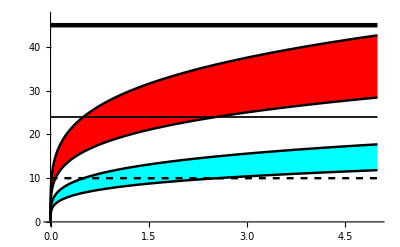

```mathematica
suppfig2= Show[figx1,figx2,PlotRange-> {All, {0,47}},AxesStyle->as, PlotRangePadding->None]
```

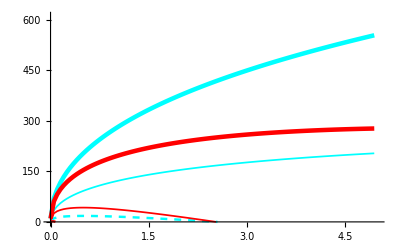

```mathematica
a1 = 1; b1 = 0.75; a2 = 20 a1; b2  = 0.75;  a3 = 1.; cSR = 1.;
allabparam = {a1, b1, a2,b2, a3, b3};
cTmax = 0.;
nowarmup = True;
free = True;
aw = 0.;

fe[z_,Trise_,ρ_ ]:=EnTime[z, trise,Trise, Trise +cTmax,ρ, trise,tf,allabparam, nowarmup,free ,aw,cSR];

nstep = 100;

data1 = Table[Flatten@{z,fe[z,Trise1, eps[[1]]]},{z,0.001,5.,5/nstep}];
data2 = Table[Flatten@{z,fe[z,Trise1,eps[[2]]]},{z,0.001,5.,5/nstep}];
data3 = Table[Flatten@{z,fe[z,Trise1, eps[[3]]]},{z,0.001,5.,5/nstep}];
data4 = Table[Flatten@{z,fe[z,Trise2, eps[[1]]]},{z,0.001,5.,5/nstep}];
data5 = Table[Flatten@{z,fe[z,Trise2, eps[[2]]]},{z,0.001,5.,5/nstep}];
data6 = Table[Flatten@{z,fe[z,Trise2, eps[[3]]]},{z,0.001,5.,5/nstep}];

pse = {{AbsoluteThickness[th],Dashed, Cyan},{AbsoluteThickness[th-0.5], Cyan},{AbsoluteThickness[th+1.5], Cyan},{AbsoluteThickness[th],Dashed, Red},{AbsoluteThickness[th-0.5], Red},{AbsoluteThickness[th+1.5], Red}};

suppfig3 = ListLinePlot[{data1,data2,data3,data4,data5,data6},PlotRange->{{0,5},{0,610}},AxesOrigin-> {0,0},PlotStyle->pse,AxesStyle-> as,PlotRangePadding->None]
```

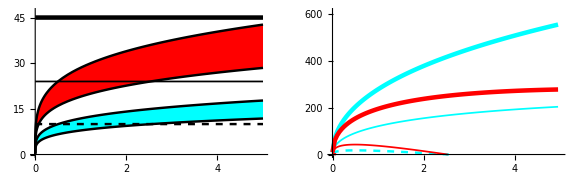

```mathematica
appfig = GraphicsRow[{suppfig2,suppfig3},ImageSize->Large]
```

```mathematica
Export["C:\\Users\\tramiada\\Documents\\Projects\\energy_budget\\ms_fig\\appendix_fig.pdf",appfig]
```

C:\Users\tramiada\Documents\Projects\energy_budget\ms_fig\appendix_fig.pdf

## Senstivity analyzes for Figure 3 (compile the main code before running this)

```mathematica
tx = {{0.01,0.1,1,10},{0,5,10,15,20,25,30}};
vect = Flatten[{Range[0.01,0.1,0.01],Range[0.2,2,0.1],Range[3,10,1]}];
```

#### with respect to convection

```mathematica
data11= Table[findTminEndo[z,rK1 = 1.,rK2 = 0.1,free =True,aw = 0.,cSR =0.25], {z, vect}];
data21= Table[findTminEndo[z,rK1 = 1.,rK2 = 0.1,free = False,aw = 0.,cSR =0.25], {z, vect}];
data31= Table[findTminEndo[z,rK1 =  1.,rK2 = 0.1,free = False,aw = 1.25,cSR =0.25], {z, vect}];

data12= Table[findTminEndo[z,rK1 = 1.,rK2 = 1.,free =True,aw = 0.,cSR =0.25], {z, vect}];
data22= Table[findTminEndo[z,rK1 = 1.,rK2 = 1.,free = False,aw = 0.,cSR =0.25], {z, vect}];
data32= Table[findTminEndo[z,rK1 =  1.,rK2 = 1.,free = False,aw = 1.25,cSR =0.25], {z, vect}];

data13= Table[findTminEndo[z,rK1 = 1.,rK2 = 10.,free =True,aw = 0.,cSR =0.25], {z, vect}];
data23= Table[findTminEndo[z,rK1 = 1.,rK2 = 10.,free = False,aw = 0.,cSR =0.25], {z, vect}];
data33= Table[findTminEndo[z,rK1 =  1.,rK2 = 10.,free = False,aw = 1.25,cSR =0.25], {z, vect}];
```

```mathematica
psa = {{Dashed,Black,AbsoluteThickness[th]},{Black,AbsoluteThickness[th]},{Black,AbsoluteThickness[2 th]}};
```

```mathematica
suppfig31 = ListLogLinearPlot[{data11,data12,data13},Joined->True,PlotRange-> {{0.01,10}, {-1,32}},AxesOrigin-> {0.01,-1},PlotStyle->psa,AxesStyle->as,ImageSize->Medium, PlotRangePadding->0.0, Ticks->tx];

suppfig32 = ListLogLinearPlot[{data21,data22,data23},Joined->True,PlotRange-> {{0.01,10}, {-1,32}},AxesOrigin-> {0.01,-1},PlotStyle->psa,AxesStyle->as,ImageSize->Medium, PlotRangePadding->0.0, Ticks->tx];

suppfig33 = ListLogLinearPlot[{data31,data32,data33},Joined->True,PlotRange-> {{0.01,10}, {-1,32}},AxesOrigin-> {0.01,-1},PlotStyle->psa,AxesStyle->as,ImageSize->Medium, PlotRangePadding->0.0, Ticks->tx];
```

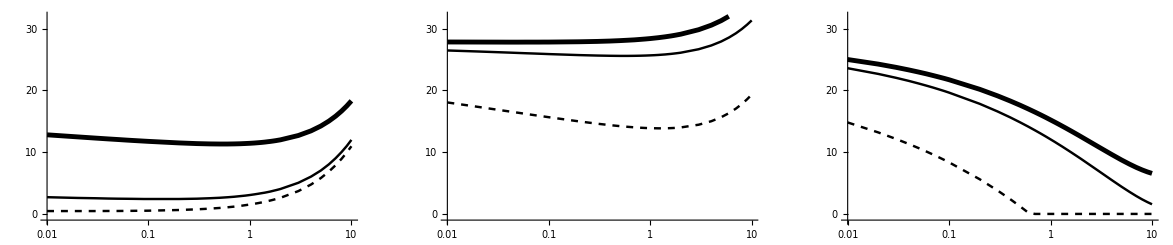

```mathematica
GraphicsRow[{suppfig31,suppfig32,suppfig33}]
```

#### with respect to conductance

```mathematica
data11= Table[findTminEndo[z,rK1 = 0.1,rK2 = 1.,free =True,aw = 0.,cSR =0.25], {z, vect}];
data21= Table[findTminEndo[z,rK1 = 0.1,rK2 = 1.,free = False,aw = 0.,cSR =0.25], {z, vect}];
data31= Table[findTminEndo[z,rK1 =  0.1,rK2 = 1.,free = False,aw = 1.25,cSR =0.25], {z, vect}];

data12= Table[findTminEndo[z,rK1 = 1.,rK2 = 1.,free =True,aw = 0.,cSR =0.25], {z, vect}];
data22= Table[findTminEndo[z,rK1 = 1.,rK2 = 1.,free = False,aw = 0.,cSR =0.25], {z, vect}];
data32= Table[findTminEndo[z,rK1 =  1.,rK2 = 1.,free = False,aw = 1.25,cSR =0.25], {z, vect}];

data13= Table[findTminEndo[z,rK1 = 10.,rK2 = 1.,free =True,aw = 0.,cSR =0.25], {z, vect}];
data23= Table[findTminEndo[z,rK1 = 10.,rK2 = 1.,free = False,aw = 0.,cSR =0.25], {z, vect}];
data33= Table[findTminEndo[z,rK1 =  10.,rK2 = 1.,free = False,aw = 1.25,cSR =0.25], {z, vect}];
```

```mathematica
psa = {{Dashed,Black,AbsoluteThickness[th]},{Black,AbsoluteThickness[th]},{Black,AbsoluteThickness[2 th]}};
```

```mathematica
suppfig34 = ListLogLinearPlot[{data11,data12,data13},Joined->True,PlotRange-> {{0.01,10}, {-1,32}},AxesOrigin-> {0.01,-1},PlotStyle->psa,AxesStyle->as,ImageSize->Medium, PlotRangePadding->0.0, Ticks->tx];

suppfig35 = ListLogLinearPlot[{data21,data22,data23},Joined->True,PlotRange-> {{0.01,10}, {-1,32}},AxesOrigin-> {0.01,-1},PlotStyle->psa,AxesStyle->as,ImageSize->Medium, PlotRangePadding->0.0, Ticks->tx];

suppfig36 = ListLogLinearPlot[{data31,data32,data33},Joined->True,PlotRange-> {{0.01,10}, {-1,32}},AxesOrigin-> {0.01,-1},PlotStyle->psa,AxesStyle->as,ImageSize->Medium, PlotRangePadding->0.0, Ticks->tx];
```

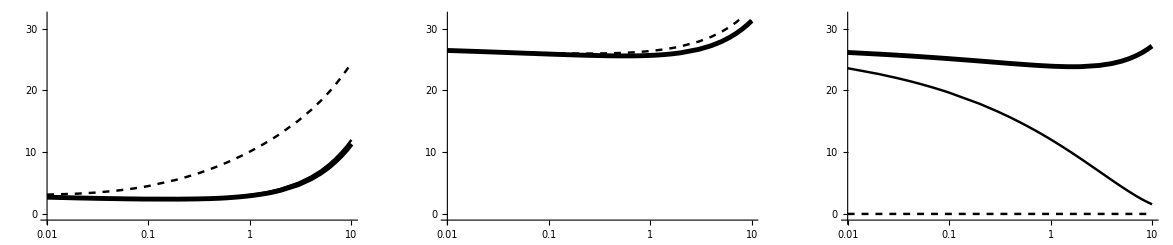

```mathematica
GraphicsRow[{suppfig34,suppfig35,suppfig36}]
```

#### with respect to radiation intensity

```mathematica
data11= Table[findTminEndo[z,rK1 = 1.,rK2 = 0.1,free =True,aw = 0.,cSR =0.5], {z, vect}];
data21= Table[findTminEndo[z,rK1 = 1.,rK2 = 0.1,free = False,aw = 0.,cSR =0.5], {z, vect}];
data31= Table[findTminEndo[z,rK1 =  1.,rK2 = 0.1,free = False,aw = 1.25,cSR =0.5], {z, vect}];

data12= Table[findTminEndo[z,rK1 = 1.,rK2 = 0.1,free =True,aw = 0.,cSR =0.75], {z, vect}];
data22= Table[findTminEndo[z,rK1 = 1.,rK2 = 0.1,free = False,aw = 0.,cSR =0.75], {z, vect}];
data32= Table[findTminEndo[z,rK1 =  1.,rK2 = 0.1,free = False,aw = 1.25,cSR =0.75], {z, vect}];

data13= Table[findTminEndo[z,rK1 = 1.,rK2 = 0.1,free =True,aw = 0.,cSR =1.], {z, vect}];
data23= Table[findTminEndo[z,rK1 = 1.,rK2 = 0.1,free = False,aw = 0.,cSR =1.], {z, vect}];
data33= Table[findTminEndo[z,rK1 =  1.,rK2 = 0.1,free = False,aw = 1.25,cSR =1.], {z, vect}];
```

```mathematica
psa = {{Dashed,Black,AbsoluteThickness[th]},{Black,AbsoluteThickness[th]},{Black,AbsoluteThickness[2 th]}};
```

```mathematica
suppfig37 = ListLogLinearPlot[{data11,data12,data13},Joined->True,PlotRange-> {{0.01,10}, {-1,32}},AxesOrigin-> {0.01,-1},PlotStyle->psa,AxesStyle->as,ImageSize->Medium, PlotRangePadding->0.0, Ticks->tx];

suppfig38 = ListLogLinearPlot[{data21,data22,data23},Joined->True,PlotRange-> {{0.01,10}, {-1,32}},AxesOrigin-> {0.01,-1},PlotStyle->psa,AxesStyle->as,ImageSize->Medium, PlotRangePadding->0.0, Ticks->tx];

suppfig39 = ListLogLinearPlot[{data31,data32,data33},Joined->True,PlotRange-> {{0.01,10}, {-1,32}},AxesOrigin-> {0.01,-1},PlotStyle->psa,AxesStyle->as,ImageSize->Medium, PlotRangePadding->0.0, Ticks->tx];
```

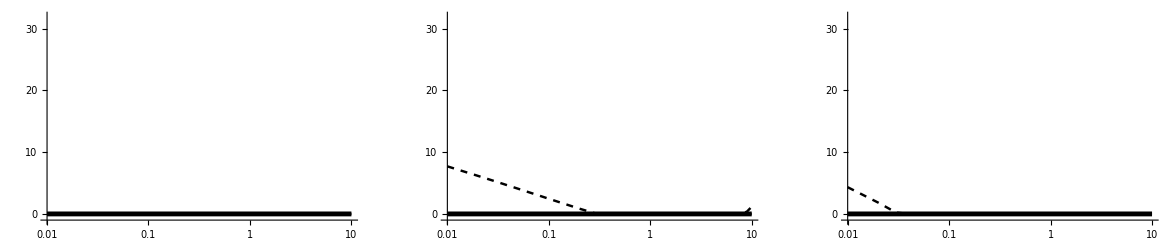

```mathematica
GraphicsRow[{suppfig37,suppfig38,suppfig39}]
```

#### panel B

```mathematica
tx = {{0,2,4,6,8,10},{{0.0,"0.0"},{0.5,"0.5"},{1.0,"1.0"},{1.5,"1.5"}}};

trise = SunRise[day,lat];
free = True;
rK2 = 1; rK1 = 1; cSR = 1;

endtf= 16 ;

data1 = Table[{z,Wtime[z, rK1,rK2,trise,endtf,free = True, trise , Trise = 10,Tmax = 10,aw = 0.,cSR]},{z,vect}];
data2 = Table[{z,Wtime[z, rK1,rK2,trise,endtf,free = True, trise , Trise = 20,Tmax = 20,aw = 0., cSR]},{z,vect}];

data3 = Table[{z,Wtime[z, rK1,rK2,trise,endtf,free = True, trise , Trise = 10,Tmax = 10,aw = 1.25,cSR]},{z,vect}];
data4 = Table[{z,Wtime[z, rK1,rK2,trise,endtf,free = True, trise , Trise = 20,Tmax = 20,aw = 1.25,cSR]},{z,vect}];
```

```mathematica
psb = {{Dashed,GrayLevel[gl],AbsoluteThickness[th]},{Dashed,Black,AbsoluteThickness[th]},{GrayLevel[gl],AbsoluteThickness[2 th]},{Black,AbsoluteThickness[2 th]}};
```

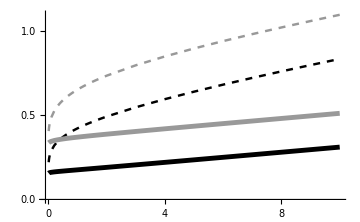

```mathematica
fig3b = ListPlot[{data1,data2,data3,data4},Joined->True,(*PlotRange-> {{-0.1,10}, {0.,All}},*)PlotStyle-> psb,AxesStyle->as,ImageSize->Medium,PlotRangePadding->0.0,AxesOrigin->{-0.1,0}, Ticks->tx]
```

#### With wind

```mathematica
trise = SunRise[day,lat];
free = True;
rK2 = 1; rK1 = 1;

endtf= 16 ;

data1 = Table[{z,Wtime[z, rK1,rK2,trise,endtf,free = False, trise , Trise = 10,Tmax = 10,aw = 0.]},{z,vect}];
data2 = Table[{z,Wtime[z, rK1,rK2,trise,endtf,free = False, trise , Trise = 20,Tmax = 20,aw = 0.]},{z,vect}];

data3 = Table[{z,Wtime[z, rK1,rK2,trise,endtf,free = False, trise , Trise = 10,Tmax = 10,aw = 1.25]},{z,vect}];
data4 = Table[{z,Wtime[z, rK1,rK2,trise,endtf,free = False, trise , Trise = 20,Tmax = 20,aw = 1.25]},{z,vect}];
```

```mathematica
psb = {{Dashed,GrayLevel[gl],AbsoluteThickness[th]},{Dashed,Black,AbsoluteThickness[th]},{GrayLevel[gl],AbsoluteThickness[2 th]},{Black,AbsoluteThickness[2 th]}};
```

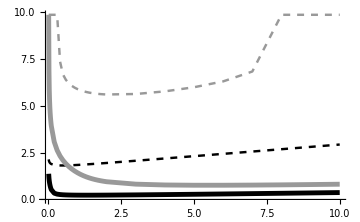

```mathematica
fig3b = ListPlot[{data1,data2,data3,data4},Joined->True,PlotRange-> {{Automatic,10}, {0.,All}},PlotStyle-> psb,AxesStyle->as,ImageSize->Medium,PlotRangePadding->0.0,AxesOrigin->{-0.1,0}]
```

#### all panels

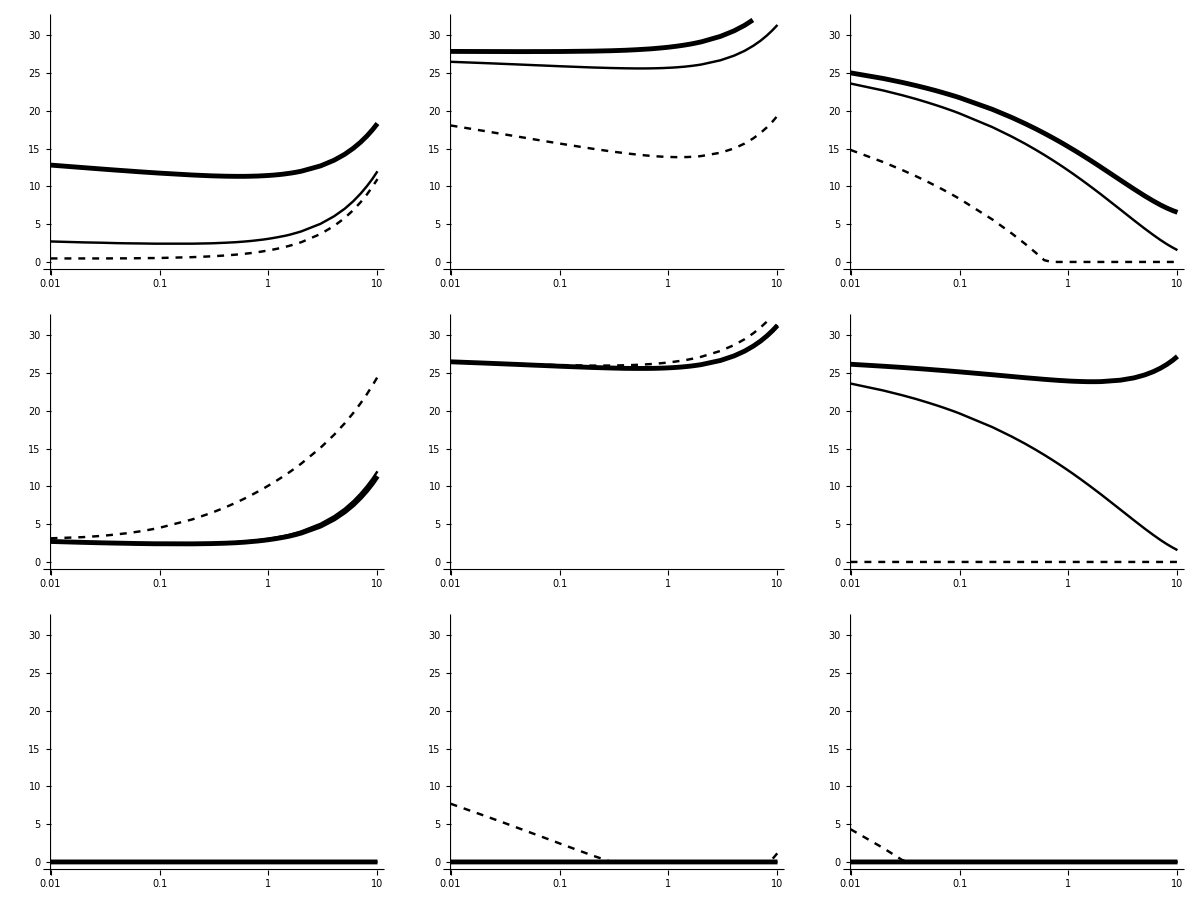

```mathematica
suppfig3 = Grid[{{suppfig31,suppfig32,suppfig33},{suppfig34,suppfig35,suppfig36},{suppfig37,suppfig38,suppfig39}},Spacings->{1,1}]
```

```mathematica
Export["C:\\Users\\tramiada\\Documents\\Projects\\energy_budget\\ms_fig\\supp_fig3.pdf",suppfig3];
```

## Supplementary file for Figure 5 (increase by 10 degree celsius)

```mathematica
a1 = 1; b1 = 0.75; a2 = 10 a1; b2  = 0.75;  a3 = 1; cSR = 0.5;

rho = 24;
cTmax = 10.;
RR =30.;
nowarmup = False;
free = True;
aw = 1.25;

tf = 1.;
zz2 = 2;
zz1= 0.5;
tstart  = trise + 0.5;
step = 0.5;
```

### panel A

```mathematica
allabparam = {a1, b1, a2,b2, a3, b3 = 1.25};
```

#### For endotherm

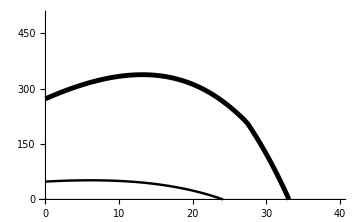

```mathematica
fA[Trise_, zz_]:=EnTime[zz, trise,Trise, Trise +cTmax,rho, tstart,tf,allabparam, False,True,aw =1.25,cSR];

data1 = Table[Flatten@{temp,fA[temp,zz1]},{temp,0,40,step}];
data2 = Table[Flatten@{temp,fA[temp, zz2]},{temp,0,40,step}];

fig5a = ListLinePlot[{data1,data2},PlotRange->{{0,40},{0,500}},ImageSize->Medium,AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None]
```

#### For ectotherm (for comparison)

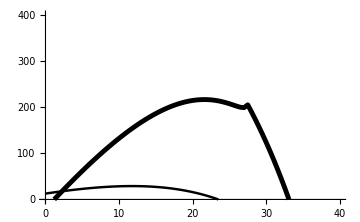

```mathematica
fA1[Trise_, zz_]:=EnTime[zz, trise,Trise, Trise +cTmax,rho, tstart,tf,allabparam, False,True,aw =0.,cSR];

step = 0.5;
data1 = Table[Flatten@{temp,fA1[temp,zz1]},{temp,0,40,step}];
data2 = Table[Flatten@{temp,fA1[temp, zz2]},{temp,0,40,step}];

fig5a1 = ListLinePlot[{data1,data2},PlotRange->{{0,40},{0,400}},ImageSize->Medium,AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None]
```

### panel B

```mathematica
allabparam = {a1, b1, a2,b2, a3, b3 = 0.5};
```

#### For endotherm

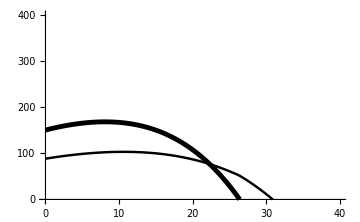

```mathematica
fB[Trise_, zz_]:=EnTime[zz, trise,Trise, Trise +cTmax,rho, tstart,tf,allabparam, False,True,aw = 1.25,cSR];

step = 0.5;
data1 = Table[Flatten@{temp,fB[temp,zz1]},{temp,0,40,step}];
data2 = Table[Flatten@{temp,fB[temp, zz2]},{temp,0,40,step}];

fig5b= ListLinePlot[{data1,data2},PlotRange->{{0,40},{0,400}},ImageSize->Medium,AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None]
```

#### For ectotherm

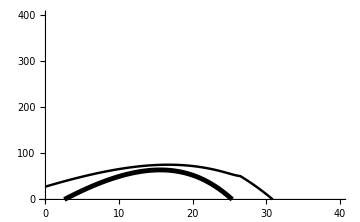

```mathematica
fB1[Trise_, zz_]:=EnTime[zz, trise,Trise, Trise +cTmax,rho, tstart,tf,allabparam, False,True,aw =0.,cSR];

step = 0.5;
data1 = Table[Flatten@{temp,fB1[temp,zz1]},{temp,0,40,step}];
data2 = Table[Flatten@{temp,fB1[temp, zz2]},{temp,0,40,step}];

fig5b1 = ListLinePlot[{data1,data2},PlotRange->{{0,40},{0,400}},ImageSize->Medium,AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None]
```

### panel C

```mathematica
RR = 30;
```

```mathematica
a1 = 1; b1 = 0.75; a2 = 10 a1; b2  = 0.75;  a3 = 1; b3 = 0.75 ;cSR = 0.5;
allabparam = {a1, b1, a2,b2, a3, b3};
rho= 24;
cTmax = 10.;
RR =30.;
nowarmup = False;
free = True;

ZZ = {0.2,2};
TF1 = Table[Min[ftf[ZZ[[i]],RR,a3,b3],ftf[ZZ[[i]],ZZ[[i]]*50,a3,b3]],{i,2}];
```

#### For endotherm

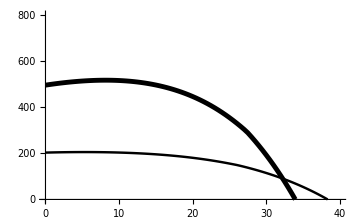

```mathematica
fC[Trise_,i_]:=EnTime[ZZ[[i]], trise,Trise, Trise +cTmax,rho, tstart,TF1[[i]],allabparam, False,True,aw =1.25,cSR];

step = 0.5;
data1 = Table[Flatten@{temp,fC[temp,1]},{temp,0,40,step}];
data2 = Table[Flatten@{temp,fC[temp,2]},{temp,0,40,step}];

 
fig5c = ListLinePlot[{data1,data2(*,data3,data4*)},PlotRange->{{0,40},{0,800}},ImageSize->Medium,AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None]
```

#### For ectotherm

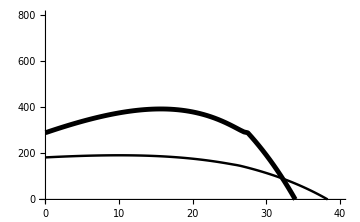

```mathematica
fC1[Trise_,i_]:=EnTime[ZZ[[i]], trise,Trise, Trise +cTmax,rho, tstart,TF1[[i]],allabparam, False,True,aw =0.,cSR];

step = 0.5;
data1 = Table[Flatten@{temp,fC1[temp,1]},{temp,0,40,step}];
data2 = Table[Flatten@{temp,fC1[temp,2]},{temp,0,40,step}];

 
fig5c1 = ListLinePlot[{data1,data2},PlotRange->{{0,40},{0,800}},ImageSize->Medium,AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None]
```

### panel D

```mathematica
RR = 15;

TF2 = Table[Min[ftf[ZZ[[i]],RR,a3,b3],ftf[ZZ[[i]],ZZ[[i]]*50,a3,b3]],{i,2}];
```

#### For endotherm

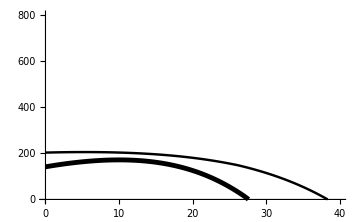

```mathematica
fD[Trise_,i_]:=EnTime[ZZ[[i]], trise,Trise, Trise +cTmax,rho, tstart,TF2[[i]],allabparam, False,True,aw = 1.25,cSR];

data1 = Table[Flatten@{temp,fD[temp,1]},{temp,0,40,step}];
data2 = Table[Flatten@{temp,fD[temp,2]},{temp,0,40,step}];

 
fig5d = ListLinePlot[{data1,data2},PlotRange->{{0,40},{0,800}},ImageSize->Medium,AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None]
```

#### For ectotherm

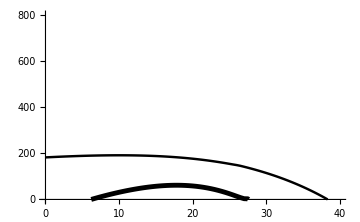

```mathematica
fD1[Trise_,i_]:=EnTime[ZZ[[i]], trise,Trise, Trise +cTmax,rho, tstart,TF2[[i]],allabparam, False,True,aw = 0.,cSR];

data1 = Table[Flatten@{temp,fD1[temp,1]},{temp,0,40,step}];
data2 = Table[Flatten@{temp,fD1[temp,2]},{temp,0,40,step}];

 
fig5d1 = ListLinePlot[{data1,data2},PlotRange->{{0,40},{0,800}},ImageSize->Medium,AxesOrigin-> {0,0},PlotStyle->ps,AxesStyle-> as,PlotRangePadding->None]
```

### all panels

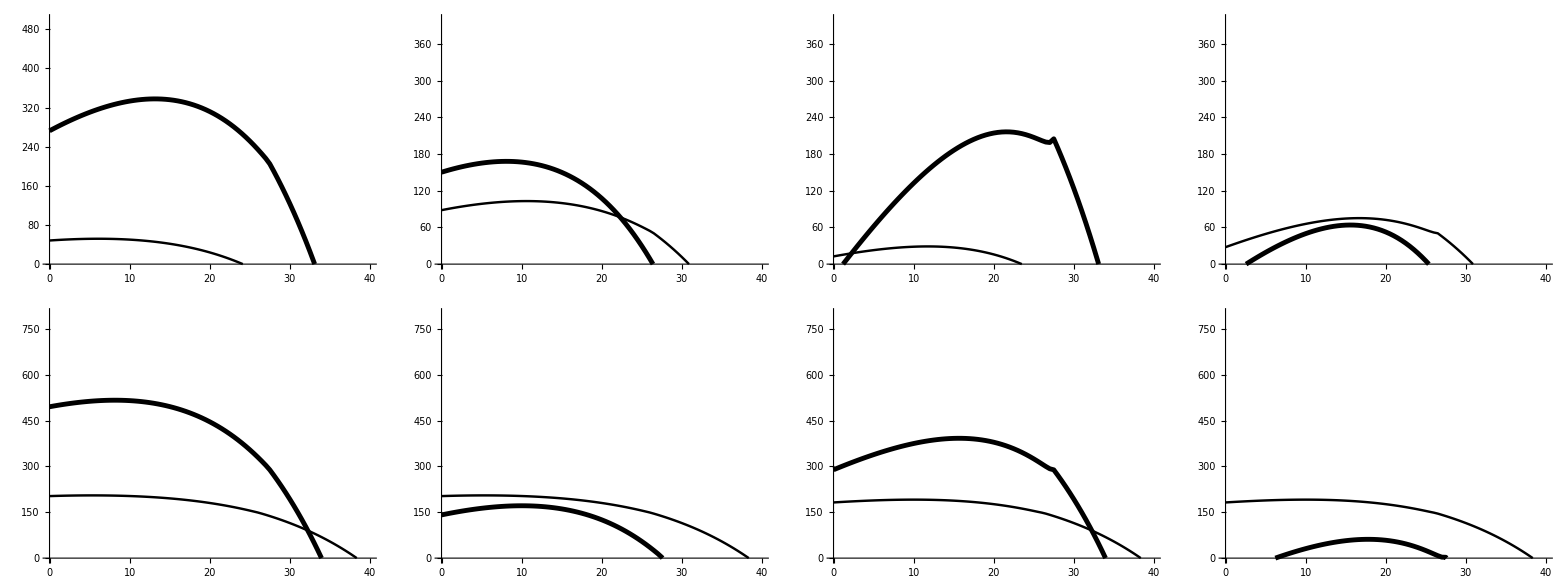

```mathematica
suppfig5 = Grid[{{fig5a,fig5b, fig5a1,fig5b1}, {fig5c,fig5d, fig5c1,fig5d1}},Spacings->{3->5,10}]
```

```mathematica
Export["C:\\Users\\tramiada\\Documents\\Projects\\energy_budget\\ms_fig\\supp_fig5.pdf",fig5];
```